## Study the sampled parameters

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
transPars=Import["saturationSamplingVaringK.csv"];
pars=Transpose[transPars];
```

```mathematica
us=pars[[Flatten[Position[transPars[[15]],_?(#>0.7&)]]]];
usLow=us[[Flatten[Position[Transpose[us][[19]],_?(0.001<#<0.01&)]]]];
usLowKm2=Flatten[usLow[[Ordering[Transpose[usLow][[15]],-1]]]];
usHigh=us[[Flatten[Position[Transpose[us][[19]],_?(100<#<1000&)]]]];
usHighKm2=Flatten[usHigh[[Ordering[Transpose[usHigh][[15]],-1]]]];
{adaptive}=pars[[Ordering[transPars[[16]],1]]];
```

```mathematica
adaptive
```

{0.00111024,32.4769,0.00378618,490.06,310.887,0.0190213,4.36647,0.801677,54.9959,0.252128,0.00209582,0.0001,0.1,1,2.75192×10^-7,0.,7,29255.7,0.634425,0.183598,0.00458448}

```mathematica
usHighKm2
```

{39.5449,129.548,0.00226326,1.30018,374.219,0.00160961,0.00128101,34.4634,941.982,0.0443539,9.12169,0.0001,0.1,1,0.944968,0.,78738,3.27602,287.822,26903.3,0.0000470857}

```mathematica
usLowKm2
```

{2.86769,0.00793878,132.57,897.756,0.884833,0.30931,11.0637,35.7494,0.00285284,0.00433867,0.0208157,0.0001,0.1,1,0.886248,0.120839,20192,46.2315,0.00133014,3.23123,1.52083}

### Now get the dynamics of enzymes in ultrasensitive networks and adaptive network

```mathematica
SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
```

```mathematica
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];

totK=0.0001;totP=0.1;totS=1;
stepNum=50;

Block[{ts,totT,xT,transAdToUsPars,usVsAd,maxPars},
maxPars=Solve[Array[k,10]==usLowKm2[[Range[10]]]];
Block[{ssthreshold},
totT=1.*10^(RandomReal[]*6-3);

Block[{tPer,step,us,ad,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->1.*10^(-4+0.1*step)}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];
p=Evaluate[x[2][ts-0.001]/.sol];
psp=Evaluate[x[6][ts-0.001]/.sol];
pt=Evaluate[x[9][ts-0.001]/.sol];
k=Evaluate[x[1][ts-0.001]/.sol];
ks=Evaluate[x[5][ts-0.001]/.sol];
kt=Evaluate[x[8][ts-0.001]/.sol];
];
];
];
];
```

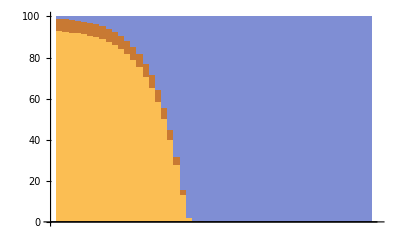

```mathematica
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile"]
```

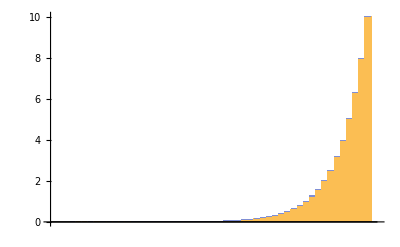

```mathematica
BarChart[Transpose[{k,kt,ks}],ChartLayout->"Stacked"]
```

```mathematica
pt
```

{0.0668845,0.0669246,0.0669357,0.0669145,0.0667997,0.066383,0.0658735,0.0652333,0.0644289,0.063419,0.0621522,0.0605635,0.0585743,0.0560876,0.0529836,0.0491171,0.0443191,0.0383853,0.0310886,0.0221902,0.0117143,0.00327934,0.00140058,0.00118313,0.00100436,0.000874343,0.000781555,0.00071446,0.000665381,0.000628917,0.000601422,0.000580405,0.000564141,0.000551411,0.000541342,0.000533295,0.0005268,0.000521506,0.000517149,0.000513526,0.000510482,0.000507883,0.000505461,0.000503023,0.000500547,0.000498034,0.000495484,0.000492894,0.000490257,0.000487557,0.000484835}

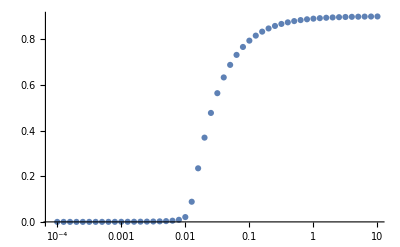

```mathematica
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

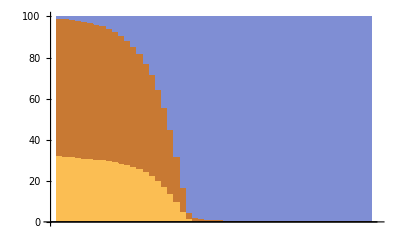

```mathematica
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile"]
```

```mathematica
pt
```

{0.00153678,0.00161561,0.00168433,0.00174753,0.00180673,0.00186249,0.0019149,0.00196386,0.00200897,0.0020497,0.00208535,0.002115,0.00213751,0.00215147,0.00215509,0.00214616,0.00212189,0.00207861,0.00201124,0.00191048,0.0017388,0.00116875,0.000702446,0.000449017,0.00030868,0.000227049,0.000176623,0.000144769,0.000123524,0.000108864,0.0000984586,0.0000909113,0.0000853162,0.0000811108,0.0000779113,0.0000754519,0.0000735455,0.0000720569,0.0000708868,0.0000699618,0.0000692261,0.0000686374,0.0000681624,0.0000677706,0.0000673962,0.0000670171,0.0000666317,0.0000662411,0.0000658482,0.0000654473,0.0000650405}

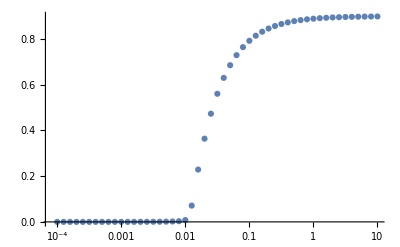

```mathematica
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

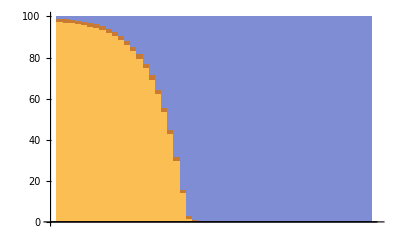

```mathematica
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile"]
```

### Now get the dynamics of enzymes in ultrasensitive networks and adaptive network

```mathematica
SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
```

```mathematica
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];

totK=0.0001;totP=0.1;totS=1;
stepNum=50;

Block[{ts,totT,xT,transAdToUsPars,usVsAd,maxPars},
maxPars=Solve[Array[k,10]==usHighKm2[[Range[10]]]];
Block[{ssthreshold},
totT=1.*10^(RandomReal[]*6-3);

Block[{tPer,step,us,ad,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->1.*10^(-4+0.1*step)}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];
p=Evaluate[x[2][ts-0.001]/.sol];
psp=Evaluate[x[6][ts-0.001]/.sol];
pt=Evaluate[x[9][ts-0.001]/.sol];
k=Evaluate[x[1][ts-0.001]/.sol];
ks=Evaluate[x[5][ts-0.001]/.sol];
kt=Evaluate[x[8][ts-0.001]/.sol];
];
];
];
];
```

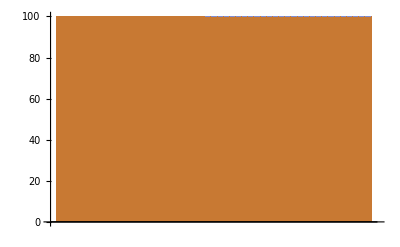

```mathematica
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile"]
```

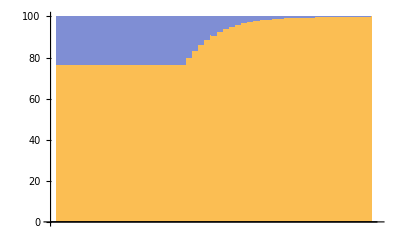

```mathematica
BarChart[Transpose[{k,kt,ks}],ChartLayout->"Percentile"]
```

```mathematica
kt
```

{3.05619×10^-10,3.86008×10^-10,4.87199×10^-10,6.14589×10^-10,7.74965×10^-10,9.76881×10^-10,1.23107×10^-9,1.55107×10^-9,1.95394×10^-9,2.46112×10^-9,3.09961×10^-9,3.90343×10^-9,4.91539×10^-9,6.18938×10^-9,7.79325×10^-9,9.81241×10^-9,1.23544×10^-8,1.55547×10^-8,1.95837×10^-8,2.4656×10^-8,3.10425×10^-8,3.9081×10^-8,4.92001×10^-8,6.19392×10^-8,7.79769×10^-8,9.81671×10^-8,1.23585×10^-7,1.55584×10^-7,1.95869×10^-7,2.46584×10^-7,3.10431×10^-7,3.90809×10^-7,4.91999×10^-7,6.19389×10^-7,7.79763×10^-7,9.81661×10^-7,1.23583×10^-6,1.55582×10^-6,1.95865×10^-6,2.46578×10^-6,3.10421×10^-6,3.90793×10^-6,4.91973×10^-6,6.19347×10^-6,7.79697×10^-6,9.81557×10^-6,0.0000123567,0.0000155556,0.0000195823,0.0000246512,0.0000310317}

```mathematica
ks
```

{0.0000301316,0.0000380348,0.0000479844,0.0000605099,0.000076278,0.0000961282,0.000121117,0.000152574,0.000192174,0.000242023,0.000304771,0.000383756,0.000483174,0.000608307,0.000765796,0.000963992,0.0012134,0.0015272,0.00192199,0.00241856,0.00304305,0.00313029,0.00313185,0.0031338,0.00313624,0.00313928,0.00314309,0.00314785,0.00315378,0.00316115,0.00317031,0.00318162,0.00319554,0.00321255,0.00323318,0.00325793,0.00328725,0.00332137,0.0033602,0.00340308,0.0034486,0.00349438,0.00353712,0.00357278,0.00359733,0.00360758,0.0036021,0.00358167,0.00354901,0.003508,0.00346276}

```mathematica
k
```

{0.0000987897,0.000124683,0.000157281,0.000198319,0.000249982,0.000315023,0.000396905,0.000499988,0.000629762,0.000793138,0.000998817,0.00125775,0.00158373,0.00199412,0.00251077,0.0031612,0.00398005,0.00501093,0.00630876,0.00794268,0.00999986,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.}

```mathematica
BarChart[Transpose[{k,kt,ks}],ChartLayout->"Stacked"]
```

-Graphics-

```mathematica
psp
```

{8.42637×10^-12,1.98659×10^-11,3.53778×10^-11,5.61587×10^-11,8.40662×10^-11,1.21474×10^-10,1.71407×10^-10,2.37853×10^-10,3.26046×10^-10,4.42876×10^-10,5.97278×10^-10,1.06391×10^-9,1.07164×10^-9,1.4242×10^-9,1.89012×10^-9,2.50316×10^-9,3.30578×10^-9,4.3698×10^-9,5.78474×10^-9,7.69067×10^-9,1.07142×10^-8,0.0000586748,0.000113881,0.000158675,0.000194866,0.000224008,0.000247409,0.00026616,0.000281157,0.000293136,0.000302693,0.000310311,0.00031638,0.000321213,0.000325059,0.00032812,0.000330555,0.000332495,0.000334039,0.000335271,0.000336256,0.000337045,0.00033768,0.000338195,0.000338614,0.000338957,0.00033924,0.000339473,0.000339664,0.000339822,0.000339951}

```mathematica
p
```

{0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0987026,0.0986439,0.0985887,0.0985439,0.0985077,0.0984786,0.0984552,0.0984364,0.0984214,0.0984094,0.0983999,0.0983923,0.0983862,0.0983814,0.0983775,0.0983745,0.098372,0.0983701,0.0983685,0.0983673,0.0983663,0.0983655,0.0983649,0.0983644,0.098364,0.0983636,0.0983633,0.0983631,0.0983629,0.0983628,0.0983626}

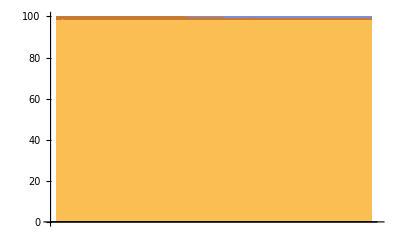

```mathematica
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile"]
```

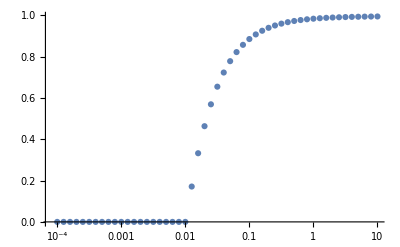

```mathematica
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

```mathematica
psp
```

{4.01506×10^-16,9.41535×10^-16,1.67728×10^-15,2.66295×10^-15,3.98664×10^-15,5.76095×10^-15,8.12936×10^-15,1.1281×10^-14,1.54641×10^-14,2.10055×10^-14,2.83291×10^-14,3.79913×10^-14,5.0715×10^-14,6.75251×10^-14,8.96246×10^-14,1.18702×10^-13,1.56772×10^-13,2.07241×10^-13,2.74355×10^-13,3.65324×10^-13,5.05979×10^-13,2.96413×10^-9,5.68297×10^-9,7.84263×10^-9,9.55811×10^-9,1.09208×10^-8,1.20032×10^-8,1.2863×10^-8,1.3546×10^-8,1.40885×10^-8,1.45195×10^-8,1.48618×10^-8,1.51338×10^-8,1.53499×10^-8,1.55216×10^-8,1.56581×10^-8,1.57666×10^-8,1.58529×10^-8,1.59217×10^-8,1.59766×10^-8,1.60205×10^-8,1.60557×10^-8,1.60842×10^-8,1.61073×10^-8,1.61264×10^-8,1.61421×10^-8,1.61552×10^-8,1.61663×10^-8,1.61757×10^-8,1.61838×10^-8,1.61909×10^-8}

```mathematica
pt
```

{0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742,0.00129742}

```mathematica
p
```

{4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67988×10^-6,4.67989×10^-6,4.67989×10^-6,4.67989×10^-6,4.67989×10^-6,4.67989×10^-6,4.6799×10^-6,4.6799×10^-6,4.67991×10^-6,4.67991×10^-6,4.67992×10^-6,4.67994×10^-6,4.67995×10^-6,4.67997×10^-6,4.67999×10^-6,4.68002×10^-6,4.68005×10^-6,4.6801×10^-6,4.68016×10^-6,4.68023×10^-6,4.68032×10^-6,4.68043×10^-6,4.68057×10^-6,4.68075×10^-6,4.68098×10^-6,4.68126×10^-6,4.68162×10^-6}

```mathematica
pt
```

{0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953,0.0999953}

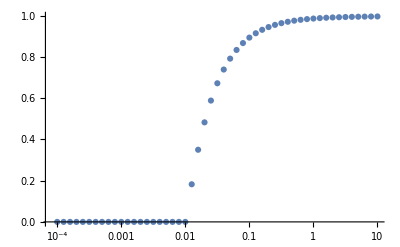

```mathematica
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

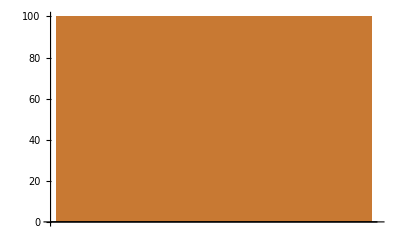

```mathematica
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile"]
```

## Test